## Initial Value

```mathematica
Clear["Global`*"]
```

```mathematica
Plot[h[t_*10^-12],{t,0,800},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1}]
```

-Graphics-

```mathematica
-Graphics-
Fc= 200*10^12 ;(*搬送波の周波数[Hz]*)
Print[Fc, "Hz"]
```

-Graphics-

200000000000000Hz

```mathematica
c[i]= Sin[2*Pi*Fc*i]
```

Sin[400000000000000 i π]

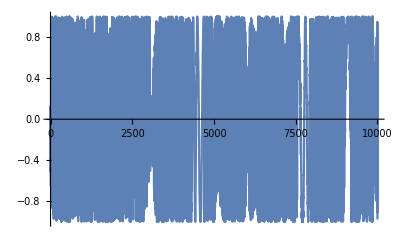

```mathematica
Plot[c[i], {i,0,10000 }]
```

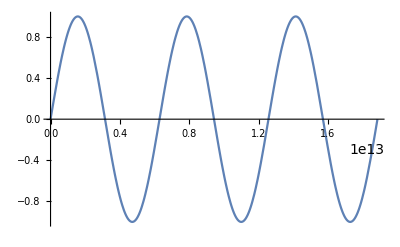

```mathematica
Plot[Sin[x*10^-12],{x,0,6*10^12 Pi}]
```

```mathematica
Plot[c[i*10^-12],{i,0,100 },PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},
BaseStyle->{Bold,FontSize->15},PlotRange->{-1,1}]
```

-Graphics-

Cos[399980000000000 i π]+Cos[400020000000000 i π]+Sin[400000000000000 i π]

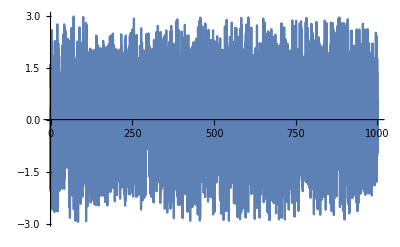

```mathematica
AM[i]=c[i]+ Cos[2Pi(Fc+10*10^9)i]+Cos[2Pi(Fc-10*10^9)i]
Plot[AM[i],{i,0,1000},PlotPoints->100]
```

```mathematica
AM[i]=c[i]+ Cos[2Pi(Fc+10*10^9)i]+Cos[2Pi(Fc-10*10^9)i]
Plot[AM[i],{i,0,1000},PlotPoints->100]
```

c[i]+Cos[2 (-10000000000+Fc) i π]+Cos[2 (10000000000+Fc) i π]

-Graphics-

## Initial Value

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
y=38.25*10^-3;(*mm*)
t[l_]:=l/c*(nm+ng);(*s*)
total=t[y];
initial=1000;
pitch=50*10^-6;(*um*)
pitchmm=pitch*10^3;
Δt=pitch*(nm+ng)/(3*10^8);
sumw=(total+Δt*initial)/Δt  ;
polnumber=1+IntegerPart[sumw]-initial;
electrodelength=N[pitch*polnumber];
electrodelengthmm=electrodelength*10^3;
Print[β2,"ps^2/km"]
Print[total*10^12,"ps"]
Print[Δt*10^12,"ps"]
Print[sumw,"point"]
Print["Rev pattern is", polnumber,"point"]
Print["electrodelength is",electrodelength*10^3,"mm"]
Print[electrodelengthmm,"mm"]
```

2.03931×10^-23ps^2/km

784.125ps

1.025ps

1765.point

Rev pattern is765point

electrodelength is38.25mm

38.25mm

```mathematica
(*For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]*)
digital[1]=0;
digital[2]=1;
digital[3]=0;digital[4]=1;digital[5]=1;digital[6]=0;digital[7]=1;digital[8]=1;digital[9]=1;digital[10]=0;digital[11]=0;digital[12]=0;digital[13]=1;digital[14]=0;digital[15]=0;digital[16]=1;digital[17]=0;digital[18]=0;digital[19]=1;digital[20]=1;digital[21]=0;digital[22]=1;digital[23]=1;digital[24]=1;digital[25]=1;

rm=Table[digital[t],{t,1,25}]
step1[t_,i_]:=If[digital[i]==1,If[i*25*10^-12<t<(i+1)*25*10^-12,1,0],If[i*25*10^-12<t<(i+1)*25*10^-12,0,0]]
signal[t_]:=signal[t]=∑_(i=1)^bit step1[t,i]
Plot[signal[t*10^-12],{t,0,bit*25},PlotStyle->{Red,Thick},Frame->True,FrameLabel->{"Time[ps]","Power"},BaseStyle->{Bold,FontSize->15},PlotRange->{0,1.1}]
```

{0,1,0,1,1,0,1,1,1,0,0,0,1,0,0,1,0,0,1,1,0,1,1,1,1}

Plot::plln: {t,0,25 bit}の範囲指定値25 bitは機械サイズの実数ではありません．

Plot[signal[t/10^12],{t,0,bit 25},PlotStyle→{Red,Thick},Frame→True,FrameLabel→{Time[ps],Power},BaseStyle→{Bold,FontSize→15},PlotRange→{0,1.1}]

```mathematica
bit=25;
For[i=1;j=0,i≤bit,i++,
For[m=j;random=RandomChoice[{0,1}],j≤m+1,j=j+1,digital[j]=random]]

rm=Table[digital[t],{t,1,bit}]
```

{0,1,1,1,1,0,0,0,0,0,0,1,1,1,1,0,0,0,0,0,0,1,1,1,1}

```mathematica
f[x]=5x
Plot[f[x*10],{x,0,1000}]
```

5 x

-Graphics-

Cos[400000000000000 π t]

Sin[t]

0

1

0

1

Cos[400000000000000 π t] Sin[t]

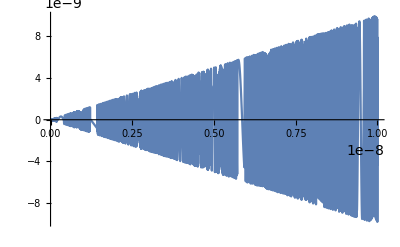

```mathematica
Fc= 200*10^12 ;(*搬送波の周波数[Hz]*)
carrier[t]= Cos[2*Pi*Fc*t]
signal[t]=Sin[t]
signal1[0]=0
signal1[1]=1
signal1[2]=0
signal1[3]=1
cs2[t]=carrier[t]*signal[t]
Plot[cs2[t],{t,0,10000*10^-12}]
```

Set::write: h xのタグTimesはProtectedです．

ⅇ^(ⅈ x)

2.03931×10^-23

ⅇ^((0.+1.01965×10^-21 ⅈ) (-1.2161×10^15+w)^2)

1. Cos[0.+1.01965×10^-21 (-1.2161×10^15+w)^2]

SetDelayed::write: Re[H_cmp[w]]のタグReはProtectedです．

$Failed

-Graphics-

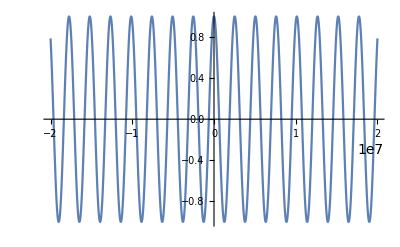

7.80437×10^19 ⅇ^(-ⅈ (-π/4+1.01965×10^-21 t^2))

(0.+0. ⅈ)+7.80437×10^19 Cos[0.785398-2.45182×10^20 t^2]

-Graphics-

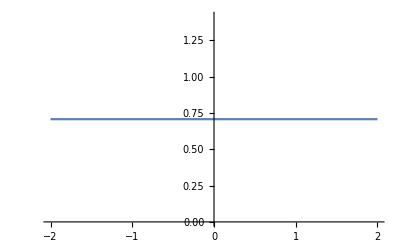

```mathematica
L=100;(*km*)
bit=25;
λ=1.55*10^-6;(*m*)
d=16;(*ps/km・nm*)
c=3*10^8;
β2=d/(2*Pi*c)λ^2*10^-3;
nm=3.96;(*電気信号の実効屈折率*)
ng=2.19;(*光波の群屈折率*)
c=3*10^8;
w2=2*Pi*c/λ;
h(x)=Exp[I*x]
β2
H_cmp[w]=Exp[1/2*β2*I*L(w-w2)^2]
ComplexExpand[Re[Exp[1/2*β2*I*L(w-w2)^2]]]
Re[H_cmp[w]]:=Cos [1/2 * β2*L(w-w2)^2]
Plot[Exp[w],{w,0,200}]
Plot[Cos [1/2 * β2*L*(w-w2)^2],{w,-200*10^5,200*10^5}]
h_cmp[t]=1/(2*Pi*β2*L)*Exp[-I*((t^2)/2*β2*L-Pi/4)]
ComplexExpand[Re[1/(2*Pi*β2*L)*Exp[-I*((t^2)/(2*β2*L)-Pi/4)]]]
Plot[ComplexExpand[Re[1/(2*Pi*β2*L)*Exp[-I*((t^2)/(2*β2*L)-Pi/4)]]],{t,-200*10^-11,200*10^-11}]
Plot[Cos[0.7853981633974483-t^(2)*1.0196526687420762*^-21 ],{t,-200*10^-12,200*10^-12}]
```